```mathematica
SetDirectory[NotebookDirectory[]];
```

## Tools

```mathematica
CutLow[lower_,list_,source_]:=For[i=1,i≤Length[source],++i,If[sizes⟦i⟧≥lower,AppendTo[newsizes,sizes⟦i⟧],Null]]
```

```mathematica
CutHigh[higher_,list_,source_]:=For[i=1,i≤Length[source],++i,If[sizes⟦i⟧≤higher,AppendTo[newsizes,sizes⟦i⟧],Null]]
```

## Import data

```mathematica
distribution=Import["distribution.csv"];
```

```mathematica
dims=Import["dims.csv"];
totalSites=dims⟦1⟧⟦1⟧dims⟦2⟧⟦1⟧;
```

```mathematica
sites=Table[distribution⟦i⟧⟦1⟧,{i,1,Length[distribution]}];
counts=Table[distribution⟦i⟧⟦2⟧,{i,1,Length[distribution]}];
```

## Analysis

```mathematica
sum=0;
total=Total[distribution]⟦2⟧;
cumulative={};
For[i=1,i<Length[distribution],++i,AppendTo[cumulative,{distribution⟦i⟧⟦1⟧,total-sum+distribution⟦i⟧⟦2⟧}];sum=sum+distribution⟦i⟧⟦2⟧]
```

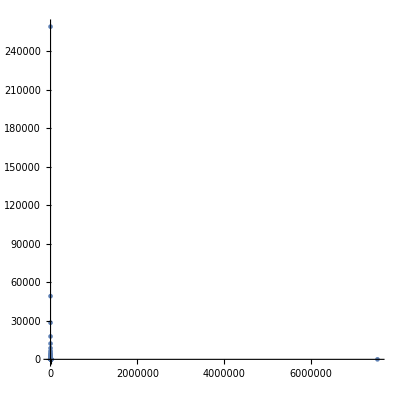

```mathematica
ListPlot[distribution,PlotRange->All,AspectRatio->1]
```

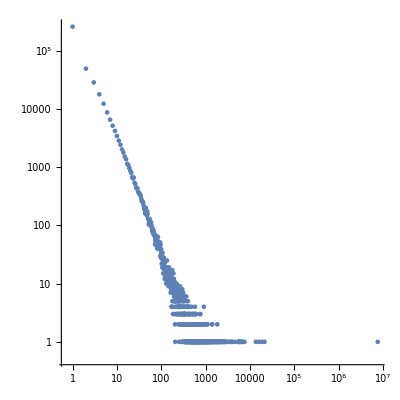

```mathematica
ListLogLogPlot[distribution,PlotRange->All,AspectRatio->1]
```

Cumulative plot

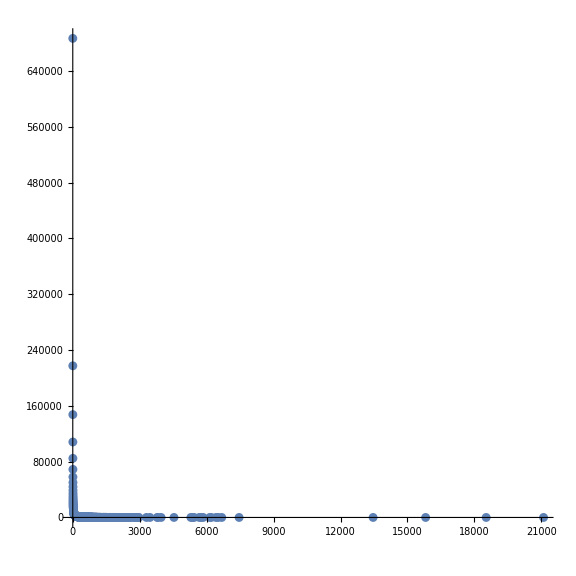

```mathematica
ListPlot[cumulative,ImageSize->Large,PlotRange->All,AspectRatio->1]
```

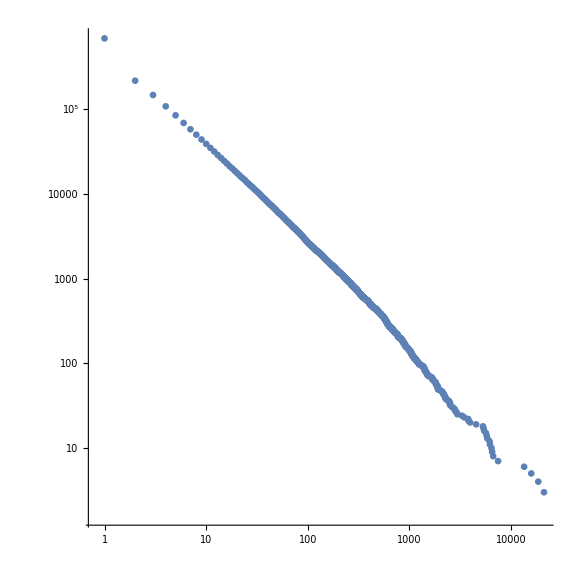

```mathematica
ListLogLogPlot[cumulative,ImageSize->Large,PlotRange->All,AspectRatio->1]
```

Plot of [ Size of cluster vs. Fraction of the total volume clusters of this size comprise ]

```mathematica
volume=Table[{distribution⟦i⟧⟦1⟧,(distribution⟦i⟧⟦1⟧*distribution⟦i⟧⟦2⟧)/totalSites},{i,1,Length[distribution]}];
```

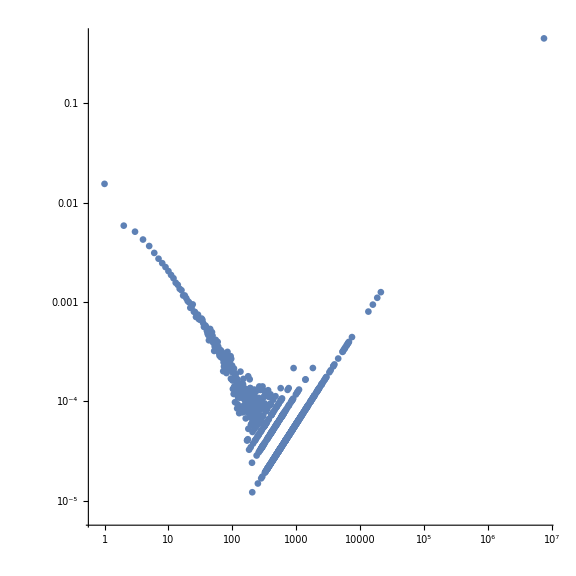

```mathematica
ListLogLogPlot[volume,ImageSize->Large,PlotRange->All,AspectRatio->1]
```

```mathematica
sum=0;
totalV=Total[volume]⟦2⟧;
cumulativeVolume={};
For[i=1,i<Length[volume],++i,AppendTo[cumulativeVolume,{volume⟦i⟧⟦1⟧,totalV-sum+volume⟦i⟧⟦2⟧}];sum=sum+volume⟦i⟧⟦2⟧]
```

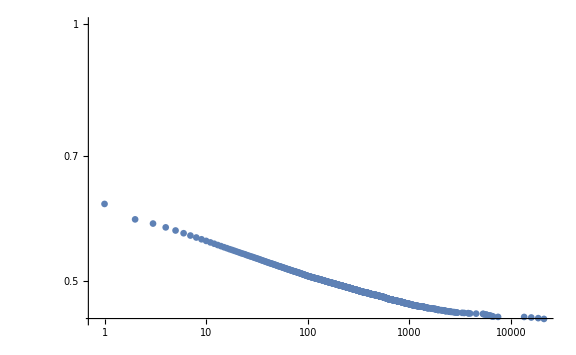

```mathematica
ListLogLogPlot[cumulativeVolume,PlotRange->{0,1},ImageSize->Large]
```

#### Portion of the volume taken up by the top 10% and top 1% of clusters

```mathematica
top10=distribution⟦Length[distribution]-Floor[0.1*Length[distribution]];;⟧;
top01=distribution⟦Length[distribution]-Floor[0.01*Length[distribution]];;⟧;
topSite=Max[sites];
```

```mathematica
Total[top10]⟦1⟧/totalSites//N
Total[top01]⟦1⟧/totalSites//N
topSite/totalSites//N
```

0.465481

0.454426

0.449089

#### The fraction of the volume taken up by the top X percent of site sizes

```mathematica
volFraction=Table[
(Total[distribution⟦i;;⟧]⟦1⟧)/(Total[distribution]⟦1⟧),
{i,1,Length[distribution]}];
```

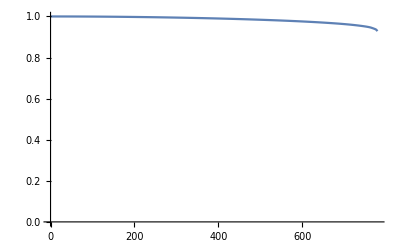

```mathematica
ListLinePlot[volFraction,PlotRange->{0,1}]
```

```mathematica
Max[sites]
```

7534460

```mathematica
aveSize=Sum[distribution⟦i⟧⟦1⟧*distribution⟦i⟧⟦2⟧,{i,1,Length[distribution]}]/Total[counts]//N
```

23.556

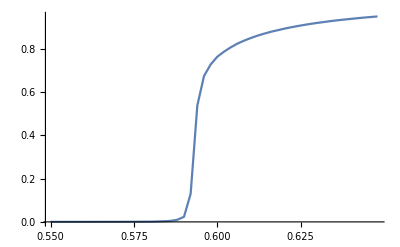

```mathematica
maxCluster1={{0.55,0.000102916},{0.552,0.000119348},{0.554,0.00011222},{0.556,0.000143647},{0.558,0.000156728},{0.56,0.000160439},{0.562,0.000200673},{0.564,0.000210801},{0.566,0.000263781},{0.568,0.000324648},{0.57,0.00033253},{0.572,0.000454608},{0.574,0.000595122},{0.576,0.000694382},{0.578,0.000888585},{0.58,0.00107006},{0.582,0.00192361},{0.584,0.00303075},{0.586,0.0046745},{0.588,0.00976921},{0.59,0.0233975},{0.592,0.129929},{0.594,0.536886},{0.596,0.672919},{0.598,0.726475},{0.6,0.762241},{0.602,0.785502},{0.604,0.805146},{0.606,0.82249},{0.608,0.836137},{0.61,0.848273},{0.612,0.859103},{0.614,0.868317},{0.616,0.877015},{0.618,0.884087},{0.62,0.89133},{0.622,0.897701},{0.624,0.903427},{0.626,0.908787},{0.628,0.913779},{0.63,0.918275},{0.632,0.922322},{0.634,0.926572},{0.636,0.930199},{0.638,0.933521},{0.64,0.936647},{0.642,0.939834},{0.644,0.942722},{0.646,0.945323},{0.648,0.9479}};
ListLinePlot[maxCluster1]
```

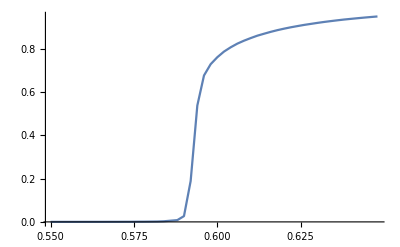

```mathematica
maxCluster2={{0.55,9.95345*10^-05},{0.552,0.000116315},{0.554,0.000118718},{0.556,0.000146856},{0.558,0.000147502},{0.56,0.000185246},{0.562,0.000205039},{0.564,0.000218667},{0.566,0.00024},{0.568,0.000350246},{0.57,0.000353032},{0.572,0.000503545},{0.574,0.000525045},{0.576,0.000830354},{0.578,0.000917228},{0.58,0.00128725},{0.582,0.00167242},{0.584,0.00285198},{0.586,0.00556234},{0.588,0.00817834},{0.59,0.0267031},{0.592,0.188447},{0.594,0.536879},{0.596,0.675528},{0.598,0.727695},{0.6,0.759872},{0.602,0.785853},{0.604,0.80554},{0.606,0.822495},{0.608,0.836108},{0.61,0.8481},{0.612,0.859206},{0.614,0.868171},{0.616,0.876838},{0.618,0.884656},{0.62,0.891522},{0.622,0.897822},{0.624,0.903392},{0.626,0.908817},{0.628,0.913483},{0.63,0.918154},{0.632,0.922495},{0.634,0.926405},{0.636,0.930135},{0.638,0.933656},{0.64,0.936715},{0.642,0.939715},{0.644,0.94259},{0.646,0.945283},{0.648,0.947863}};
ListLinePlot[maxCluster2]
```

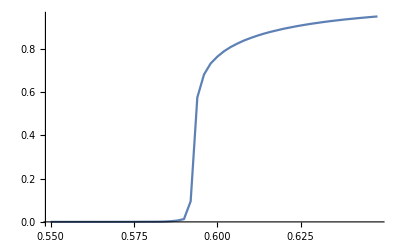

```mathematica
maxCluster3={{0.55,4.64646*10^-05},{0.552,5.01643*10^-05},{0.554,5.87389*10^-05},{0.556,6.50823*10^-05},{0.558,7.41521*10^-05},{0.56,8.40032*10^-05},{0.562,0.000102705},{0.564,9.79764*10^-05},{0.566,0.000123764},{0.568,0.000151581},{0.57,0.000176055},{0.572,0.000225363},{0.574,0.000285123},{0.576,0.000390636},{0.578,0.000660661},{0.58,0.000749991},{0.582,0.000838025},{0.584,0.00143061},{0.586,0.00310155},{0.588,0.00613218},{0.59,0.0130305},{0.592,0.0949519},{0.594,0.574162},{0.596,0.679985},{0.598,0.731153},{0.6,0.76242},{0.602,0.787385},{0.604,0.80692},{0.606,0.822774},{0.608,0.836997},{0.61,0.84868},{0.612,0.859393},{0.614,0.868789},{0.616,0.87714},{0.618,0.884431},{0.62,0.891712},{0.622,0.89769},{0.624,0.903592},{0.626,0.908868},{0.628,0.913875},{0.63,0.918308},{0.632,0.922634},{0.634,0.926597},{0.636,0.930153},{0.638,0.933693},{0.64,0.936783},{0.642,0.939837},{0.644,0.942717},{0.646,0.945463},{0.648,0.947969}};
ListLinePlot[maxCluster3]
```

```mathematica
diff=Table[{maxCluster2⟦i⟧⟦1⟧,maxCluster3⟦i⟧⟦2⟧-maxCluster2⟦i⟧⟦2⟧},{i,1,Length[maxCluster3]}];
```

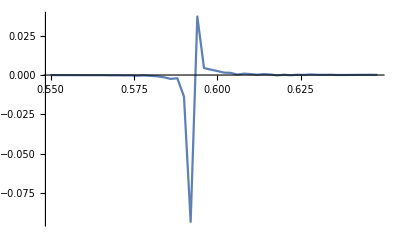

```mathematica
ListLinePlot[diff,PlotRange->All]
```